Calculate equivalence classes of list, and return indices grouped by equivalence class

```mathematica
EquivalenceIndices[list_,f_]:=Module[{matchingPairs,graph,components},matchingPairs = Select[Tuples[Range[Length[list]],2],
f[list⟦#⟦1⟧⟧,list⟦#⟦2⟧⟧]&];
graph = Graph[Apply[UndirectedEdge,matchingPairs,{1}]];
ConnectedComponents[graph]
];
```

### Example sequences

```mathematica
genSeq=StringJoin[RandomChoice[{"112","102","012","002"},8000]];
```

```mathematica
seqGen[{a_,b_}] := RandomChoice[{Mod[a +b,2],Mod[a+b+1,2]}]
seqLen = 2000;
init = {1,1};
genSeq=StringJoin[ToString/@Transpose[NestList[{#⟦2⟧,seqGen[#]}&,init,seqLen]]⟦1⟧];
```

Generate binary sequence from binning the logistic map

```mathematica
logistic[x_,r_] := r x (1-x);
seqLen = 6000;
genSeq=StringJoin[If[#>0.5,"1","0"]&/@NestList[logistic[#,3.6]&,0.6,seqLen]];
```

Generate sequence from Fibonacci sequence modulo n

```mathematica
seqLen = 6000;
genSeq = StringJoin [ToString /@ (Mod[Fibonacci[#],4]&/@Range[seqLen])];
StringTake[genSeq,50]
```

11231011231011231011231011231011231011231011231011

### Build tree from sequence

```mathematica
(*Build tree from sequence*)
seq = genSeq;
seqLen = StringLength[seq];
L = 8;
subSeqs = Table[StringTake[seq,{i,i+L-1}],{i,seqLen-L+1}];
treeData=Function[{subSeq},
subStrings=StringTake[subSeq,#]&/@Range[0,L];
{Take[subStrings,{1,-2}],Take[subStrings,{2,-1}]}
]/@subSeqs;
tree=TreeGraph[(#⟦1⟧-> #⟦2⟧)&/@DeleteDuplicates[Transpose[(Flatten/@Transpose[treeData])]]
,VertexLabels->"Name"];
Print[VertexCount[tree]]
```

332

Build ϵ-machine from tree using depth subL subtrees

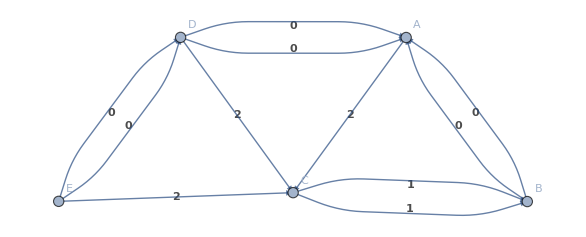

(A->C | B->A | B->A | C->B | C->B | D->A | D->A | D->C | E->C | E->D | E->D
2 | 0 | 1 | 1 | 0 | 0 | 1 | 2 | 2 | 0 | 1)

```mathematica
vertices = VertexList[tree];
subL = 4;
(*To determine the depth of the subtree, we compare the subtree of depth subL to the subtree of depth subL-1. If the tree depth is in fact smaller than subL, the vertex list will be identical. VertexOutComponent does not behave correctly for depth zero, so the conditional returns the root node if the depth is 0*)
{subTreeRoots,subTreeVertices }=Transpose[Select[
Transpose[
{vertices,VertexOutComponent[tree,#,subL]&/@vertices}],
(#⟦2⟧≠If[subL-1 == 0,{#⟦1⟧},VertexOutComponent[tree,#⟦1⟧,subL-1]])&]];
(*Remove name of root node from the name of each node, to compare tree structure*)
treeStructures=Function[{vertexList},
If[Length[vertexList]<subL+1,{},
(Function[{string},
StringDrop[string,StringLength[vertexList⟦1⟧]]]/@vertexList)]
]/@subTreeVertices;
(*Comparisons should not depend on order of vertices*)
treeStructures = Sort/@treeStructures;
equivalenceIndices=EquivalenceIndices[treeStructures,Equal];
classNames =FromCharacterCode[64+#]&/@Range[Length[equivalenceIndices]];
edgeList = {};
labelList = {};
Do[
sourceVertexIndexList = equivalenceIndices⟦sourceIndex⟧;
Function[{sourceVertexIndex},
targetVertexIndexList = equivalenceIndices⟦targetIndex⟧;
Function[{targetVertexIndex},
isEdge = EdgeQ[tree,subTreeRoots⟦sourceVertexIndex⟧-> subTreeRoots⟦targetVertexIndex⟧];
edgeList =If[isEdge,
Append[edgeList,
classNames⟦sourceIndex⟧-> classNames⟦targetIndex⟧],
edgeList
];
labelList = If[isEdge,
Append[labelList,StringTake[subTreeRoots⟦targetVertexIndex⟧,-1]],
labelList
];
]/@targetVertexIndexList
]/@sourceVertexIndexList,
{sourceIndex,Length[classNames]},{targetIndex,Length[classNames]}];
{edgeList,labelList} = Transpose[DeleteDuplicates[Transpose[{edgeList,labelList}]]];
EdgeLabeler[edgePoints_,edge_]:= {Text[Style[labelList⟦Position[edgeList,edge]⟦1,1⟧⟧,Medium,Bold,Black],Mean@edgePoints],Arrow@edgePoints};
machine=Graph[edgeList,VertexLabels->"Name",EdgeShapeFunction->EdgeLabeler];
Graph[machine]
Print[MatrixForm[{edgeList,labelList}]]
```

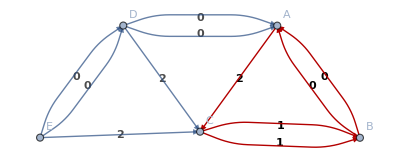

```mathematica
HighlightGraph[machine,FindCycle[machine]]
```

### Do a random walk on the graph with n steps starting from some vertex

2102002012012012112102002012112112012012

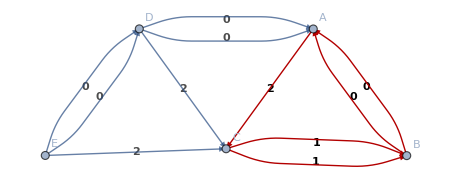

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
n = 40;
init = "A";
curVertex = init;
pathSeq = "";
pathVertexList = {};
pathEdgeList = {};
With[{machine = machine},
Do[
{edge,edgeLabel}=RandomChoice[
Cases[Transpose[{edgeList,labelList}],{curVertex->vf_,_}]
];
newVertex = edge/.(a_->b_)-> b;
pathSeq = pathSeq <> edgeLabel;
pathVertexList = Append[pathVertexList,newVertex];
pathEdgeList = Append[pathEdgeList,edge];
curVertex = newVertex;
,{i,n}]
];
pathSeq
HighlightGraph[machine,pathEdgeList]
```

```mathematica
Animate[
HighlightGraph[machine,pathEdgeList⟦i⟧],{i,1,Length[pathEdgeList],1}]
```

Delete edges from graph  to remove initial condition states (unfinished). Need to differentiate multi-edges by label, and delete orphan vertices

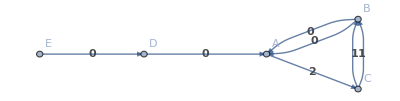

```mathematica
(*Delete vertices from graph, e.g. to remove initial condition states*)
minusInits=EdgeDelete[machine,Complement[edgeList,Union@@FindCycle[machine,{0,Length[edgeList]}]]]
```